# msBBGlink interface

```mathematica
Null
```

January 17, 2017:
A new binary that unifies my bloomberg-to-mathematica functions into a single connection, and which adds new features to the intraday functions.

A modern update to my 2009-era code that used to reside here. It newly includes (1) ability to turn DPDF setting on and off, if there are times when you want to adjust for dividends and corporate action and other times you don’t, and (2) the functions are renamed to share a common scheme with my other bloomberg-to-Mathematica functions, and (3) the ability to get intraday trades and intraday “bars” are now in a single binary, which lets you use both functions with a single persistent connection.

The interface code relies on Associations and DateObjects, so won’t work with older versions of Mathematica, but the binary accepts and returns strings, so could be used from any version of Mathematica that works with WSTP (and probably even MathLink).

This interface consists of four commands:

msBBGhistory: returns historical data from Bloomberg, normally in TemporalData format though alternatives are available. Can be used for example to retrieve U.S. CPI monthly back to 1969, or the closing price of Apple Inc. daily since 1978.
msBBGcurrent: Returns Bloomberg data for a single field for one or more securities. Works for both single-number responses (such as current market cap) and multi-field responses (such as all registered owners). The FLDS command in the Bloomberg terminal can be used to identify what data is available for each security and which overrides, if any, are allowed.
msBBGintraday: returns intraday trade data (or ask data, or bid data)
msBBGintradayBars:  returns periodic intraday data (price snapshots every minute, for example, aggregating volume from that minute).

## links

```mathematica
link1= Install[Flatten@{Drop[FileNameSplit[$InstallationDirectory],-2],"msFunctions","msBBGlink.exe"}]
```

LinkObject[…]

```mathematica
Off[Unset::norep];
If[Head[link1]===LinkObject,
Off[LinkObject::linkn];
Uninstall[link1];
Remove[link1];
];
If[Head[link1]===Symbol,Remove[link1]];
On[Unset::norep];
```

## create link

```mathematica
Options[msBBGmakeLink]={"path to executable"->Flatten@{Drop[FileNameSplit[$InstallationDirectory],-2],"msFunctions","msBBGlink.exe"}};
msBBGmakeLink[OptionsPattern[]]:=Install[OptionValue["path to executable"]];msBBGmakeLink::usage = "msBBGmakeLink[]: When run, launches the WSTP application that moves historical intraday data from Bloomberg to Mathematica. msBBGintraday[] will launch and kill this automatically, but you can do it manually with this function, assign the result to a variable, and pass the link to msBBGintraday[] with the \"LinkObject]\"→ option if you plan on calling it many times in succession.  This saves the overhead of relaunching the link for every call. When finished, can call Uninstall[(this link)] and the program will be quit. Can set \"path to executable\" variable if the default is for some reason not what you want.";
```

## intraday

```mathematica
Options[msBBGintraday]={"daylightsaving start"->{2015,3,8},"daylightsaving end"->{2015,11,1},"tick type"->"TRADE","LinkObject"->Null,"path to executable"->FileNameJoin[{NotebookDirectory[],"Debug","msBBGlink.exe"}],"output"->Association(*or List*),"use DPDF"->True,"debug"->False,"noisy"->False};msBBGintraday[ticker_String,starttime_DateObject,endtime_DateObject,OptionsPattern[]]:=Module[{output, link,st,et,daylighttimezone,dateformat,x,fld,ok,dsb,dse}, ok=True;
If[MemberQ[{"trade","bid","ask"},ToLowerCase[OptionValue["tick type"]]],fld=ToUpperCase[OptionValue["tick type"]],ok=False];
link =If[Head[OptionValue["LinkObject"]]===LinkObject,OptionValue["LinkObject"],
 Install[OptionValue["path to executable"]]]; (* set up link to C++ Code if needed *)
 dsb = DateObject[OptionValue["daylightsaving start"]]; (*Remember to reset this every year*)
dse = DateObject[OptionValue["daylightsaving end"]];(*Remember to reset this every year*)
daylighttimezone = -4;
dateformat = {"Year","-","Month","-","Day","T","Time"};
st = DateObject[starttime];
st=If[dsb≤st&&dse≥ st,DateString[DatePlus[st,{-daylighttimezone,"Hour"}],dateformat],(*else*)DateString[DatePlus[st,{-(daylighttimezone-1),"Hour"}],dateformat]];
If[OptionValue["noisy"],Print["st: ",st]];
et = DateObject[endtime];
et=If[dsb≤et&&dse≥ et,DateString[DatePlus[et,{-daylighttimezone,"Hour"}],dateformat],(*else*)DateString[DatePlus[et,{-(daylighttimezone-1),"Hour"}],dateformat]];
If[OptionValue["noisy"],Print["et: ",et]];
If[OptionValue["noisy"],Print["msBBGintradayLink arguments: ",{ticker,fld,st,et,If[OptionValue["use DPDF"],1,0],If[OptionValue["debug"],1,0]}]];
x=msBBGintradayLink[ticker,fld,st,et,If[OptionValue["use DPDF"],1,0],If[OptionValue["debug"],1,0]];
If[OptionValue["noisy"],Print["x: ",x]];
output = ToExpression[x];(*using ToExpression to convert C++ string output into list *)
output = Map[{If[dsb≤DateObject[#[[1]]]&& dse≥DateObject[#[[1]]],DatePlus[DateObject[#[[1]]],{daylighttimezone,"Hour"}],DatePlus[DateObject[#[[1]]],{daylighttimezone-1,"Hour"}]],#[[2]],#[[3]]}&,output];
output = If[OptionValue["output"]===List,output,Map[<|"Time"->#[[1]],"Price"->#[[2]],"Size"->#[[3]]|>&,output]];
output = If[OptionValue["output"]===List,output,Map[<|"Time"->#[[1]],"Price"->#[[2]],"Size"->#[[3]]|>&,output]];

If[Head[OptionValue["LinkObject"]]===LinkObject,False,Uninstall[link]]; (* close link if needed *) 
 output]

msBBGintraday::usage = 
"msBBGintraday[ticker_,starttime_,endtime_] retrieves intraday ticks from Bloomberg for a given ticker within the specified period. 
PARAMETERS:
ticker: e.g., \"AAPL Equity\"
starttime: DateObject indicating start date and time
endtime: DateObject indicating end date and time.

Bloomberg seems to save detailed intraday data back six months.

By default returns trade data, but can set option \"tick type\" to \"BID\" or \"ASK\" if you want something different.

Returns a three-member list for every datapoint available: {time, price, size}. Pass \"output\"→Association if you prefer an Association to the list. Oother optional parameters include \"daylightsaving beg\" and \"daylightsaving end\", which change every year. For a liquid security, the number of datapoints here is likely to be enormous, and you may want to consider using msBBGintradayBars[] instead.

\"LinkObject\" can be passed a link object created by msBBGmakeLink[], saving the overhead of re-launching the link. If you do this, later Uninstall[] the link.
\"path to executable\"→should be set to the correct place by default but if you have more than one version of the executable, for example, you can pick one by setting the path here.";
```

```mathematica
x=msBBGintraday["AAPL US Equity",DateObject[{2016,12,02,14,30,00}],DateObject[{2016,12,02,14,35,00}],"noisy"->False,"LinkObject"->link1]
```

{<|Time→Fri 2 Dec 2016 14:30:00GMT-5.,Price→109.81,Size→200|>,<|Time→Fri 2 Dec 2016 14:30:01GMT-5.,Price→109.8,Size→100|>,<|Time→Fri 2 Dec 2016 14:30:01GMT-5.,Price→109.8,Size→100|>,<|Time→Fri 2 Dec 2016 14:30:01GMT-5.,Price→109.8,Size→100|>,968,<|Time→Fri 2 Dec 2016 14:34:59GMT-5.,Price→109.86,Size→100|>,<|Time→Fri 2 Dec 2016 14:34:59GMT-5.,Price→109.86,Size→100|>,<|Time→Fri 2 Dec 2016 14:35:00GMT-5.,Price→109.851,Size→100|>,<|Time→Fri 2 Dec 2016 14:35:00GMT-5.,Price→109.86,Size→100|>}
 |  |  |  |

## intraday bars

```mathematica
Options[msBBGintradayBars]={"daylightsaving start"->{2017,3,8},"daylightsaving end"->{2017,11,1},"fill"->1,"tick type"->"TRADE","path to executable"->Flatten@{Drop[FileNameSplit[$InstallationDirectory],-2],"msFunctions","msBBGlink.exe"},"LinkObject"->Null,"output"->Association(*or List*),"use DPDF"->True,"debug"->False};msBBGintradayBars[ticker_String,starttime_DateObject,endtime_DateObject,barsize_/;NumberQ[barsize],OptionsPattern[]]:=Module[{output, link,st,et,x,daylighttimezone,dateformat,fld,ok,dsb,dse},
 ok=True;
If[MemberQ[{"trade","bid","ask"},ToLowerCase[OptionValue["tick type"]]],fld=ToUpperCase[OptionValue["tick type"]],ok=False];
link =If[Head[OptionValue["LinkObject"]]===LinkObject,OptionValue["LinkObject"],
 Install[OptionValue["path to executable"]]]; (* set up link to C++ Code if needed *)
 dsb = DateObject[OptionValue["daylightsaving start"]]; (*Remember to reset this every year*)
dse = DateObject[OptionValue["daylightsaving end"]];(*Remember to reset this every year*)
daylighttimezone = -4;
dateformat = {"Year","-","Month","-","Day","T","Time"};
st = DateObject[starttime];
st=If[dsb≤st&&dse≥ st,DateString[DatePlus[st,{-daylighttimezone,"Hour"}],dateformat],(*else*)DateString[DatePlus[st,{-(daylighttimezone-1),"Hour"}],dateformat]];
et = DateObject[endtime];
et=If[dsb≤et&&dse≥ et,DateString[DatePlus[et,{-daylighttimezone,"Hour"}],dateformat],(*else*)DateString[DatePlus[et,{-(daylighttimezone-1),"Hour"}],dateformat]]; 
x=msBBGintradayBarsLink[ticker,fld,st,et,barsize,OptionValue["fill"],If[OptionValue["use DPDF"],1,0],If[OptionValue["debug"],1,0]];
output = ToExpression[x];(*using ToExpression to convert C++ string output into list *)
output = Map[{If[dsb≤DateObject[#[[1]]]&& dse≥DateObject[#[[1]]],DatePlus[DateObject[#[[1]]],{daylighttimezone,"Hour"}],DatePlus[DateObject[#[[1]]],{daylighttimezone-1,"Hour"}]],#[[2]],#[[3]],#[[4]],#[[5]],#[[6]],#[[7]]}&,output];
output = If[OptionValue["output"]===List,output,Map[<|"Time"->#[[1]],"Open"->#[[2]],"High"->#[[3]],"Low"->#[[4]],"Close"->#[[5]],"Tick Counts"->#[[6]],"Shares"->#[[7]]|>&,output]];
If[Head[OptionValue["LinkObject"]]===LinkObject,False,Uninstall[link]]; (* close link if needed *) 
 output]

msBBGintradayBars::usage = 
"msBBGintradayBars[ticker_,starttime_,endtime_,barsize_] retrieves intraday samples from Bloomberg for a given ticker within the specified period. 
PARAMETERS:
ticker: e.g., \"AAPL Equity\"
starttime: DateObject indicating start date and time
endtime: DateObject indicating end date and time
barsize: is the sample frequency, in minutes
Optionally, can pass
	\"tick type\" →  \"TRADE\" or \"BID\" or \"ASK\", and/or
	\"fill\"→ If this is set to 1, the API will append previous day close information as first datapoint as the start of trading for the specified period. Otherwise, the first data point will be the actual first trading on that day.

Bloomberg seems to save detailed intraday data back six months.

Returns seven items for each bar —
1: Time
2: Open
3: High
4: Low
5: Close
6: Tick Counts per bar
7: Shares per bar

By default returns these in List format, but pass \"output\"→Association if you prefer it that way.
\"LinkObject\" can be passed a link object created by msBBGmakeLink[], saving the overhead of re-launching the link. If you do this, later Uninstall[] the link.
\"path to executable\"→should be set to the correct place by default but if you have more than one version of the executable, for example, you can pick one by setting the path here.

If you want every trade, rather than periodic samples, use msBBGintraday[].";
```

```mathematica
x=msBBGintradayBars["INDU Index",DateObject[{2016,12,02,14,30,00}],DateObject[{2016,12,02,15,30,00}],10,"LinkObject"->link1]
```

{<|Time→Fri 2 Dec 2016 14:30:00GMT-5.,Open→19158.9,High→19166.9,Low→19154.8,Close→19164.9,Tick Counts→600,Shares→0|>,<|Time→Fri 2 Dec 2016 14:40:00GMT-5.,Open→19164.6,High→19168.2,Low→19160.9,Close→19167.3,Tick Counts→600,Shares→0|>,<|Time→Fri 2 Dec 2016 14:50:00GMT-5.,Open→19167.3,High→19167.3,Low→19157.2,Close→19157.3,Tick Counts→600,Shares→0|>,<|Time→Fri 2 Dec 2016 15:00:00GMT-5.,Open→19156.8,High→19164.7,Low→19155.7,Close→19162.6,Tick Counts→600,Shares→0|>,<|Time→Fri 2 Dec 2016 15:10:00GMT-5.,Open→19162.3,High→19162.4,Low→19154.6,Close→19154.6,Tick Counts→600,Shares→0|>,<|Time→Fri 2 Dec 2016 15:20:00GMT-5.,Open→19154.6,High→19174.,Low→19154.4,Close→19173.3,Tick Counts→600,Shares→0|>}

## history

```mathematica
Options[msBBGhistory]={"adjust"->"CALENDAR","type"->"value","name"->"df","output"->"nf3"(* vs. "nf2" or "ts"*),"keep link active"->False,"noisy"->False,"use DPDF"->False,"LinkObject"->Null,"path to executable"->Flatten@{Drop[FileNameSplit[$InstallationDirectory],-2],"msFunctions","msBBGlink.exe"}};
msBBGhistory[ticker_String,field_String,start_,end_,freq_String,OptionsPattern[]]:= Module[{raw,name1,output,link, date,endS},
name1=If[OptionValue["name"]=="df",ticker<>": "<>field,OptionValue["name"]];
link =If[Head[OptionValue["LinkObject"]]===LinkObject,OptionValue["LinkObject"],
 Install[OptionValue["path to executable"]]]; (* set up link to C++ Code if needed *)
date=Switch[ToUpperCase[freq] ,"DAY","DAILY","WEEK","WEEKLY","MONTH","MONTHLY","QUARTER","QUARTERLY","YEAR","YEARLY","ANNUAL","YEARLY",_,ToUpperCase[freq]];
 endS=Switch[Head[end],List,DateString[end,{"Year","Month","Day"}],DateObject,DateString[end,{"Year","Month","Day"}],String,end];raw =msBBGhistoryLink[ticker, field,DateString[start,{"Year","Month","Day"}],If[endS=="",endS,DateString[end,{"Year","Month","Day"}]],date,ToUpperCase[OptionValue["adjust"]],If[OptionValue["use DPDF"],1,0],If[OptionValue["noisy"],1,0]]; 
output=If[OptionValue["noisy"],raw,ToExpression[raw]];(* use ToExpression to convert C++ string output into list *)
(*If[OptionValue["noisy"],Print["raw: ",raw]];*)
If[Head[OptionValue["LinkObject"]]===LinkObject,False,Uninstall[link]]; (* close link if needed *) 
Which[
!OptionValue["noisy"](*&&StringLength[output]>0*),output=Map[{Take[DateList[#[[1]]],3],#[[2]]}&,output];
output=Switch[OptionValue["type"],"value",TimeSeries[output],"pctchanges",EventSeries[output],"delta",EventSeries[output]];
output=Switch[OptionValue["output"],
"nf2",Association["name"->name1,"type"->OptionValue["type"],"data"->output],
"nf3",TemporalData[output,MetaInformation->{"name"->name1,"type"->OptionValue["type"]}],
"ts",output],
!OptionValue["noisy"]&& StringLength[output]==0,output="Data not found. For more information, run with \"noisy\"→True",
OptionValue["noisy"],output
]
];
msBBGhistory::usage = 
"msBBGhistory[ticker_,field_,start_,end_,freq_,OptionsPattern[]] retrieves data from Bloomberg for a given ticker and field within the specified period.
PARAMETERS:
ticker: e.g., \"AAPL Equity\"
field: e.g., \"Px_Last\"
start: start date
end: end date, or \"\" for current day
freq: is the data frequency. Choices: \"day\", \"week\", \"month\", \"quarter\", or \"year\"\n

Optionally, you can pass  adjust→ for the period adjustment (default is \"CALENDAR\"). Choices, \"ACTUAL\", \"CALENDAR\"
type→ is one of \"delta\", \"pctchanges\", or (by default) \"value\". 
name→\"whatever\" sets the name.
\"output\"→\"nf2\", \"nf3\" (the new default) or \"ts\". nf2 is an association with Keys \"data\", \"name\" and \"type\". nf3 is a TemporalData object with the same information in MetaInformation. \"ts\" leaves out the MetaInformation.
\"noisy\"→(True or False), toggles debugging info
\"use DPDF\"→(True or False), toggles whether or not the DPDF settings in the Bloomberg terminal are respected. This would typically be used to shut off dividend adjustment, if it has been turned on.
\"LinkObject\" can be passed a link object created by msBBGmakeLink[], saving the overhead of re-launching the link. If you do this, later Uninstall[] the link.
\"path to executable\"→should be set to the correct place by default but if you have more than one version of the executable, for example, you can pick one by setting the path here.

By default, pctchanges and delta-type data are stored as EventSeries[], while value-type data is stored as TimesSeries[]." ;
```

```mathematica
msBBGhistory["IBM US Equity","Px_Close_1D",{2015,1,1},"","Day","use DPDF"->False]
```

TemporalData[…]

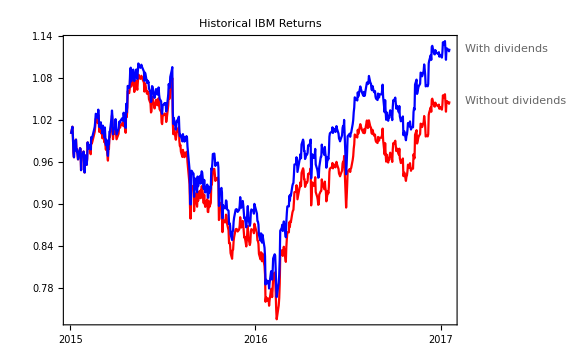

```mathematica
bbgLink=msBBGmakeLink[];
x1=msBBGhistory["IBM US Equity","Px_Close_1D",{2015,1,1},"","Day","use DPDF"->False,LinkObject->bbgLink];
x2=msBBGhistory["IBM US Equity","Px_Close_1D",{2015,1,1},"","Day","use DPDF"->True,LinkObject->bbgLink];
Uninstall[bbgLink];Remove[bbgLink];
DateListPlot[{Callout[x1/x1["FirstValue"],"Without dividends"],Callout[x2/x2["FirstValue"],"With dividends"]},PlotStyle->{Red,Blue},PlotLabel->"Historical IBM Returns",Frame->{True,True,False,False},ImageSize->Large]
```

## current

```mathematica
Options[msBBGcurrent]={"noisy"->False,"outer noisy"->False,"LinkObject"->Null,"path to executable"->Flatten@{Drop[FileNameSplit[$InstallationDirectory],-2],"msFunctions","msBBGlink.exe"},"overrides"->{}};
msBBGcurrent[ticker_,field_String,OptionsPattern[]]:=Module[{raw,exp,link,ticks,trimmed,overrides},
link =If[Head[OptionValue["LinkObject"]]===LinkObject,OptionValue["LinkObject"],
 Install[OptionValue["path to executable"]]]; (* set up link to C++ Code if needed *)
ticks=If[StringQ[ticker],ticker,StringJoin[Riffle[ticker," & "]]];
If[OptionValue["outer noisy"]||OptionValue["outer noisy"],Print["ticks: ",ticks]];
overrides=If[Length[OptionValue["overrides"]]>0,StringJoin[Riffle[Riffle[Keys[OptionValue["overrides"]],Values[OptionValue["overrides"]]]," & "]],""];
If[OptionValue["outer noisy"],Print["overrides: ",overrides, ". (head: ",Head[overrides],")"]];
raw=msBBGcurrentLink[ticks,field,If[OptionValue["noisy"],1,0],overrides];
If[OptionValue["outer noisy"],Print["raw Head: ",Head[raw],". raw: ",raw]];
If[Head[OptionValue["LinkObject"]]===LinkObject,False,Uninstall[link]]; (* close link if needed *) 
If[Head[raw]===msBBGcurrentLink,Message[msBBGcurrent::linkDead];Null,(*else*)
If[!StringContainsQ[raw,"EXCEPTION"],
trimmed=StringTrim[raw];
If[OptionValue["outer noisy"],Print["trimmed: ",trimmed]];
exp=If[!OptionValue["noisy"],ToExpression[trimmed],trimmed];
If[Head[exp]===String,raw,exp],(* else, had exception *)
raw]
]
];
msBBGcurrent::usage = "msBBGcurrent[Bloomberg ticker_String OR _List,field_String,OptionsPattern[]]. Connects to Bloomberg and downloads a single field's data for one or more securities. Fields that return multiple lines (like dividend history or current holders) will be delivered as Lists of Associations. The user may wish to wrap each of these in a Dataset.

If you plan on running msGetBB[] many times in close succession, run msBBGmakeLink[] first and save the resulting LinkObject to a variable. You can then pass that LinkObject to msGetBB[] with the \"LinkObject\"→ option, and Uninstall[] it when you are done. If you want to check multiple securities at once, pass them all to the function as a list (e.g. msGetBBG[{\"AAPL US Equity\",\"IBM US Equity\"},\"DVD_EX_DT\"]). For long lists this is about 20x faster than calling the function repeatedly. If used in this manner, the function may return the answers out of order, but will attach the security name to each datum for identification.

You can pass overrides to the function with \"overrides\"→<|\"field id 1\"→\"value 1\", \"field id 2\"→\"value two\", \"field id 3\"→\"field three\"|>}. Check the FLDS command for a security on the Bloomberg terminal to see which overrides are allowed.  You can include an arbitrary number of overrides.

Can set the \"path to executable\" variable if the default is for some reason not what you want.
\"noisy\"→True will return debugging information from both the WSTP conduit and the Mathematica interface that calls it. \"outer noisy\"→True will debugging information from only the Mathematica part.";
msBBGcurrent::linkDead="Could not connect to link. Perhaps it died before Mathematica could pass data to it.";
```

```mathematica
msBBGcurrent["C US Equity","PX_LAST"]
```

58.38

Get multiple datapoints -- if you ask for a lot of names, Bloomberg may not return the answers in order, so the WSTP interface tags each answer with the corresponding security name.

```mathematica
msBBGcurrent[{"IBM US Equity","AAPL US Equity"},"PX_LAST","LinkObject"->bbgLink]
```

{{IBM US Equity,168.18},{AAPL US Equity,119.965}}

Works with text as well as numbers.

```mathematica
msBBGcurrent["IBM US Equity","General_Counsel"]
```

"MICHELLE H BROWDY"

Works with arrays of data (which are often most conveniently stored as Datasets), and handles missing fields elegantly.

```mathematica
Dataset[msBBGcurrent["CAR US Equity","DVD_HIST_ALL"]]
```

Dataset[<>]